SECANT METHOD

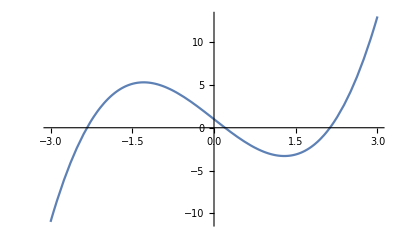

```mathematica
f[x_] :=x^3 -5x +1
Plot[f[x],{x,-3,3}]
```

```mathematica
f[x_]:=x^3-5x+1
a[0]=2.0;
a[1]=3.0;
Do[
a[n+2]=a[n+1]-((a[n+1]-a[n])/(f[a[n+1]]-f[a[n]]))*f[a[n+1]],{n,0,9}]
TableForm[Table[{n,a[n],f[a[n]]},{n,0,9}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

0 | 2. | -1.
1 | 3. | 13.
2 | 2.07143 | -0.469023
3 | 2.10376 | -0.207936
4 | 2.12952 | 0.00943116
5 | 2.1284 | -0.000175111
6 | 2.12842 | -1.42692×10^-7
7 | 2.12842 | 2.16183×10^-12
8 | 2.12842 | -1.77636×10^-15
9 | 2.12842 | -1.77636×10^-15